# LMM_Hermite.nb (v.1.0) - Lagrange Mesh Method in One-Dimension -

Authors: J.C. del Valle  &  A.V. Turbiner (delvalle@ciencias.unam.mx & turbiner@nucleares.unam.mx)

This  notebook calculates the first  eigenvalues of a one-dimensional Schrödinger equation for a given potential V(x) defined in -∞<x<∞. 
The Method used is the Lagrange-Mesh with an Hermite mesh. Details of the method can be consulted in D. Baye, Physics Reports, Volume 565, 10 March 2015, Pages 1-107.

Some generalities:

1) Input parameters are:
                                              *Coupling Constant (optional)
                                              * Dimension of the Mesh (n)
                                              *Scaling Parameter (h)
                                              *Number of desired Levels/EigenValues (NN)
                                              *One-dimensional potential
                                              

2) By default, the program calculates the first  eigenvalues of the quartic  oscillator.                      
3) The program generates a file called roots”###”.txt in the same directory that contains this notebook.         
4) Output file with first eigenvalues is generated.
4) Output file with nodes of wave function  is generated.

To charge the type of the mesh this code can be easily modified.

## Cell #0: Available Meshes

```mathematica
AvailableRoots={};
SetDirectory[NotebookDirectory[]];
Do[Do[If[FileExistsQ["roots"<>ToString[i]<>"_WP_"<>ToString[j]<>".txt"]==True,AppendTo[AvailableRoots,{i,j}]],{i,0,2020}],{j,300,300}]
If[Length[AvailableRoots]==0,Print["There are not meshes available, generate them using Cell # 1, please."],Print["I can use the following meshes:"];Do[Print[AvailableRoots[[i]][[1]]],{i,1,Length[AvailableRoots]}]]
```

I can use the following meshes:

10

25

50

75

100

150

200

250

300

400

500

1000

1900

2000

2020

## Cell #1: Definitions, Input Parameters, and Mesh

```mathematica
(* Mesh *)
λ=10;
n=500;
(* Workingpresicion/Number of digits in arithmetics *)
WP=300;
(* One-dimensional potential, it should be written in variable x*)
V[x_]:=1/2 x^2+λ x^4;
(* Scaling Parameter -rational or integer number- *)
h=1;
(* Number of desired Levels*)
NN=3;
(* Mesh *)
SetDirectory[NotebookDirectory[]];
If[
          (*Checking that file with roots does not exist*)
FileExistsQ[
                      (* ----------------------------------------------------------- *) 
                      "roots"<>ToString[n]<>"_WP_"<>ToString[WP]<>".txt"]==False,
                          (* Zeros of Hermite polinomials *)
                           sols=NSolve[HermiteH[n,x]==0,x,WorkingPrecision->WP];
                                k=0;
                          (* Asingning roots to variables *)
                                sols/.{r__Rule}:>Set@@@({r}/.var:x->Subscript[var,++k]);
                           Rlst=Table[x/.sols[[i]],{i,1,Length[sols]}];
                          (* Creating the file wth roots *)
                           Export["roots"<>ToString[n]<>"_WP_"<>ToString[WP]<>".txt",Rlst,"Table"],
                          (* ----------------------------------------------------------- *) 
                         (* If it does exists, then we import and read the file *)
                          lroots=Import[ "roots"<>ToString[n]<>"_WP_"<>ToString[WP]<>".txt","Table"];
                        (* Asingning roots to variables *)
                         Do[Subscript[x, i]=lroots[[i]][[1]],{i,1,Length[lroots]}]];
                              Clear[k];
```

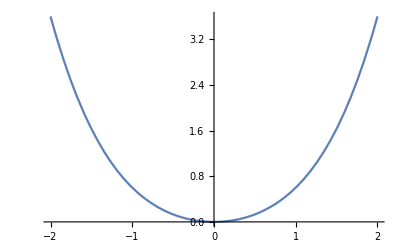

```mathematica
Plot[V[x],{x,-2,2}]
```

## Cell # 2: Main Program, Results for Energy, and Output File

```mathematica
(* Matrix Kinetic Elements *)
Do[For[i=1,i<j,i++,Subscript[T, i,j]=(-1)^(i-j)2/(Subscript[x, i]-Subscript[x, j])^2;Subscript[T, j,i]=Subscript[T, i,j]],{j,1,n}];
Clear[i];
Do[Subscript[T, i,i]=2/6(2n+1-Subscript[x, i]^2),{i,1,n}];
(* Matrix Potential Elements *)
Do[Subscript[V, i,j]=V[h Subscript[x, i]]KroneckerDelta[i,j],{i,1,n},{j,1,n}];
(* Hamiltonian Matrix *)
M=Table[Table[1/(2 h^2)Subscript[T, l,m]+Subscript[V, l,m],{m,1,n}],{l,1,n}];
(* ---------------------------------------------- *)
                    (* Preparing Output on screen *)
(* ---------------------------------------------- *)
(* Information of Mesh*)
Print["Mesh Points: ",n];
(* Approximate domain *)
Print["Approximate domain of the Wave Function: |x| ≤ ",N[Subscript[x, n] h,5]]
(*Scaling Parameter*)
Print["Scaling Parameter: ",h]
PrintTemporary["I am calculating the energy..."];
(* EigenValues *)
RES=Timing[Sort[Eigenvalues[N[M,WP],-NN,Method->"Arnoldi"]]];
En=RES[[2]];
CPUT=RES[[1]];
Print["Potential : V(x) = ", V[x]]
Do[Print[Subscript["E", i-1]," = ", En[[i]]],{i,1,Length[En]}]


(* Output file *)
fileName="LMM_Mesh_"<>ToString[n]<>".dat";
file=OpenWrite[fileName,PageWidth->Infinity];
WriteString[file," ***************************************************\n"];
WriteString[file,"                  Lagrange-Mesh Method              \n"];
WriteString[file,"***************************************************\n"];
WriteString[file,"\n"];
(* Potential *)
WriteString[file,"                    V(x) = "<>ToString[FortranForm[V[x]]]<>"\n"];
WriteString[file,"\n"];
WriteString[file,"..................................................\n"];
(*Mesh Information*)
WriteString[file,"   Mesh (dimension of the basis): "<>ToString[n]<>"\n"];
(*Scaling Parameter*)
WriteString[file,"   Scaling Parameter:             "<>ToString[h]<>"\n"];
(* CPU TIME *)
WriteString[file,"   CPU Time (sec)   :             "<>ToString[CPUT]<>"\n"];
WriteString[file," ..................................................\n "];
WriteString[file,"\n"];
(* Energy levels *)
WriteString[file,"n           Energy\n"];
WriteString[file,"\n"];
Do[
WriteString[file,""     <>ToString[i-1]<>"   "<>ToString[NumberForm[En[[i]],50]]<>"\n"];,
{i,1,Length[En]}];
WriteString[file,"\n"];
WriteString[file,"..................................................\n"];
WriteString[file,"\n"];
WriteString[file,"n: quantum number \n"];
Export[file,,"List"];
Close[file];
Print["CPU Time : " ,CPUT, " s"] 
Print["I have generated a file named: ", fileName]
```

Mesh Points: 500

Approximate domain of the Wave Function: |x| ≤ 31.051

Scaling Parameter: 1

Potential : V(x) = x^2/2+10 x^4

E_0 = 1.5049724077788910991642544490814580334423037451642501234703015136040894980130056948784122189145952352379209740902027765088551657249432289887178297998817367849977019921313207254075635181732232342571736658387249725994560731799943170897231624122827461160752187397853868866756311096700472807300805

E_1 = 5.3216082562612460034799636322387607698909604747714659636509080531408947206592647153259099460349599177379088181605614429505734330842761120034266955344180708197345045322935381346114387092241805179923630631202478564287688340658823927567577967792464928152303316152858119789686404762551788492660633

E_2 = 10.347055592460471328202166829861711765652378192678022270725590007967371074428744812210816513871761279278253226257069214845509534699342213867872357434637530481370648051376150166479568398691592105525443109325504156534620680863346583020885977557164888307495280567238630602500820809079153101021977

CPU Time : 49.2808 s

I have generated a file named: LMM_Mesh_500.dat

```mathematica
En
```

```mathematica
{0.559146327183503,1.769502643949043,3.1386243084981142}
```

{0.559146,1.7695,3.13862}

```mathematica
{0.5072562045245876,1.5356482782967902,2.59084579619069}
```

{0.507256,1.53565,2.59085}

## Cell # 3: Wave Functions

```mathematica
PrintTemporary["I am calculating the coefficients for the Eigenfunctions..."];
(* Precision for Wave Function *)
WFP=20;
(* EigenVector's Coefficient *)
Vec=Eigenvectors[N[M,WFP],-NN,Method->"Arnoldi"];
(* Avoiding too small coefficients *)
Vec=Vec/.x_/;Abs[x]≤10^-WFP->0;
(* Assignment of Coefficients *)
Do[Do[Overscript[Subscript[c, j], k]=Vec[[k]][[j]],{j,1,n}],{k,1,Length[Vec]}]
(* Normalization Constant *)
HH=√π 2^n n!;
(* Definitio of Lagrange Function *)
f[j_,y_]:=SetPrecision[(-1)^(n-j)(2HH)^(-1/2)HermiteH[n,y]/(y-Subscript[x, j])Exp[-y^2/2],WFP]
ψψ[y_,k_]:=SetPrecision[∑_(i=1)^n h Overscript[Subscript[c, i], k] f[i,y],WFP]
(* Not Normalized Wave function: note that k aquires the meaning of principal quantum number *)
ψ[y_,k_]:=SetPrecision[ψψ[y,NN-k],WFP]
Print["I am ready to construct the Wave Function of the first ", NN," low lying states"]
```

I am ready to construct the Wave Function of the first 3 low lying states

## Cell # 4: Plot of Wave Function and Nodes

Plot for Wave function with quantum number n = 2

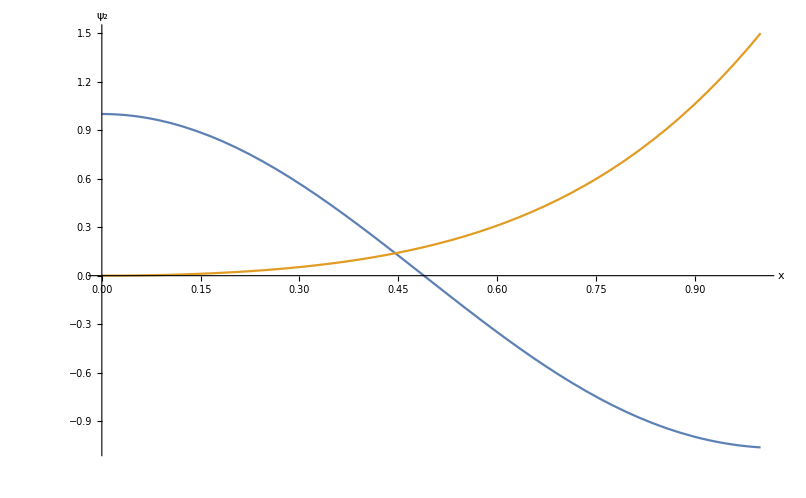

I have calculated the correct number of positive nodes: 1

Node at x= {0.48890422442405597820586487207232705895321847494699}

I have generated a file that contains the results named: Nodes_State_n_2_Basis_500.dat

```mathematica
(* Quantum Number, qn = 0, 1, 2,...,NN-1 *)
qn=2;
(* Domain for Wave Function xMIN <= x <= xMAX *)
xMIN=0;
xMAX=1;
(* Number of (uniformly distributed) points to sample the Wave Function, the larger value for "points", the higher accuracy for wave function: *)
points=100;
(* List of values for Wave Function *)
PrintTemporary["I am constructing the  wave function for quantum number n = ",qn];
L=Monitor[Table[{xMIN + (xMAX-xMIN)/points i,ψ[xMIN + (xMAX-xMIN)/points i,qn]},{i,0,points}],i];
(*  Interpolation for the Wave Function *)
ψI=Interpolation[L];
(* Plot of Wave Function*)
If[Abs[ψI[0]]≤10^-10,ψ[x_]:=ψI[x/h]/ψI'[0],ψ[x_]:=ψI[x/h]/ψI[0]]
PWF=Plot[{ψ[x],V[x]},{x,xMIN,xMAX},AxesLabel->{"x",Subscript["ψ", qn]}];
PrintTemporary["Now, I will calculate the nodes of the Wave Function ..."];
FakeNodes={};

Quiet[Do[sol=FindRoot[ψI[x],{x,RandomReal[{0,xMAX}]},WorkingPrecision->50];
             sol=sol/.x_/;Abs[x]≤10^-12->0;If[ 0<(x/.sol)<xMAX,AppendTo[FakeNodes,x/.sol]]
             ,{i,1,100}]];
Nodes = DeleteDuplicates[Sort[FakeNodes],Abs[#1-#2]<10^-6&];
Print["Plot for Wave function with quantum number n = ", qn]
Print[PWF]

If[Floor[qn/2]==Length[Nodes],Print["I have calculated the correct number of positive nodes: ", Floor[qn/2]],Print["I am sorry, I have not calculated the position of the nodes propertly. Check Cell # 3, please.","\n" ,"\n" ,"SUGGESTION: The correct position of the nodes can be found if:","\n" , "\n" ,  "i) You increase the value of points. Currently, you are using ",points," points","\n" ,  "ii) Based on the plot of the wave function, you reduce the domain (xMIN <= x <= xMAX) trying to localize the positive nodes ","\n" ] ];
Print["Node at x= ",Nodes]



fileName2="Nodes_State_n_"<>ToString[qn]<>"_Basis_"<>ToString[n]<>".dat";
file2=OpenWrite[fileName2,PageWidth->Infinity];
WriteString[file2," ***************************************************\n"];
WriteString[file2,"                  Lagrange-Mesh Method              \n"];
WriteString[file2,"***************************************************\n"];
(* Potential *)
WriteString[file2,"                    V(x) = "<>ToString[FortranForm[V[x]]]<>"\n"];
WriteString[file2,"..................................................\n"];
WriteString[file2,"   Mesh (dimension of the basis): "<>ToString[n]<>"\n"];
WriteString[file2,"   Scaling Parameter:             "<>ToString[h]<>"\n"];
WriteString[file2,"   Quantum  Number (n):           "<>ToString[qn]<>"\n"];
WriteString[file2," ..................................................\n "];
WriteString[file2,"\n"];
WriteString[file2,"             Energy (LMM) = "<>ToString[NumberForm[En[[NN-qn]],16]]<>"\n"];
WriteString[file2,"         # Positive Nodes = "<>ToString[NumberForm[Floor[qn/2],16]]<>"\n"];
WriteString[file2,"\n"];
WriteString[file2,"..................................................\n"];
WriteString[file2,"                    Nodes\n"];
WriteString[file2,"..................................................\n"];
WriteString[file2,"\n"];
Do[
    WriteString[file2,""<>ToString[NumberForm[Nodes[[i]],{20,20}]]<>"\n"];,
    {i,1,Length[Nodes]}]
Export[file2,,"List"];
Close[file2];
Print["I have generated a file that contains the results named: ", fileName2]
```